```mathematica
Clear["Global`*"]
```

It would take a good deal of time studying NDSolve to get expert results. The following is a sample of some results, some not bad, some with quite a bit of room for improvement.

Explicit Method

5.  Using numbered line (5), p. 937, with h = 1 and k = 0.5, solve the heat problem, numbered lines (1) - (3) on p. 937, to find the temperature at t = 2 in a laterally insulated bar of length 10 ft and initial temperature f(x) = x(1 - 0.1x).

The problem description referred to numbered lines in the text, and I should set those down here. Also, since the problem specifies numbered line (5),  I may need that too.

(1)  u_t=u_xx, 0≤ x≤1, t≥0
(2)  u[x,0]=f[x], (Initial condition)
(3)  u[0,t]=u[1,t]=0  , (Boundary conditions)
(5) u_(i,j+1)=(1-2 r)u_ij+r(u_(i+1,j)+u_(1-1,j)) , r=k/h^2

```mathematica
Clear["Global`*"]
```

I am redoing this problem after finishing the section. Crank-Nicolson works well and it pretty fast too. One route to Crank-Nicolson comes from the NDSolve Method Plugin Framework tutorial. The wolfram documentation uses Crank-Nicolson as an example for writing a customized plugin for NDSolve.

```mathematica
Options[CrankNicolson]={MaxIterations->5,Tolerance->Automatic};
CrankNicolson/:NDSolve`InitializeMethod[CrankNicolson,stepmode_,sd_,rhs_,state_,OptionsPattern[CrankNicolson]]:=Module[{prec,rtol,maxit},maxit=OptionValue[MaxIterations];
prec=state@"WorkingPrecision";
rtol=OptionValue[Tolerance];
If[rtol===Automatic,rtol=10^(-prec*3/4)];
CrankNicolson[maxit,rtol]]

CrankNicolson[maxit_,rtol_]["Step"[f_,h_,t0_,x0_,f0_]]:=Module[{J,LU,t1=t0+h,x1,f1,residual,err,done=False,tol=rtol,count=0},x1=x0+h f0;
f1=f[t1,x1];
x1=x0+(h/2) (f0+f1);
J=f["JacobianMatrix"[t1,x1]];
LU=IdentityMatrix[Length[x1],SparseArray]-(h/2) J;
LU=LinearSolve[LU];
While[(count≤maxit)&&!done,f1=f[t1,x1];
residual=x1-x0-(h/2)*(f0+f1);
err=Norm[residual,Infinity];
If[err<tol,done=True
(*else*),x1=x1-LU[residual];
count++;]];
If[count>maxit,Message[CrankNicolson::cvmit,maxit];
x1=$Failed];
{x1,f1}];

CrankNicolson[___]["StepInput"]={"F"["T","X"],"H","T","X","XP"};
CrankNicolson[___]["StepOutput"]={"X","XP"};
CrankNicolson[___]["DifferenceOrder"]:=2;
CrankNicolson[___]["StepMode"]:="Fixed";
```

Now comes the part where the problem function is inserted. The execution of this expression is much faster than the generic heat equation which was in the NDSolve docs.  Raising the accuracy goal above 9 does not result in an improvement in the output. If the working precision is set anywhere except where it is shown below, a warning message appears.

```mathematica
cnz=First[u/.NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],u[x,0]==x(1.-0.1x),u[0,t]==0,u[10,t]==0},u,{x,0,2},{t,0,2},Method->{"FixedStep","StepSize"->.001,Method->{CrankNicolson}},AccuracyGoal->15,WorkingPrecision->MachinePrecision]]
```

InterpolatingFunction[{{0., 10.}, {0., 2.}}, <>]

I can show a plot.

```mathematica
cnn=Plot3D[cnz[x,t],{x,0,1},{t,0,1},ImageSize->250,AspectRatio->Automatic,ViewPoint->{1000, 9000, 4000.},AxesLabel->Automatic]
```

-Graphics3D-

The table below shows pretty good agreement with the text answer. The right column is the one for comparison.

```mathematica
tableW=TableForm[Table[cnz[h,k],{h,0,10},{k,0,2}]]
```

0. | 0. | 0.
0.9 | 0.755958 | 0.667706
1.6 | 1.41136 | 1.26027
2.1 | 1.9016 | 1.7183
2.4 | 2.20015 | 2.00477
2.5 | 2.30002 | 2.10191
2.4 | 2.20015 | 2.00477
2.1 | 1.9016 | 1.7183
1.6 | 1.41136 | 1.26027
0.9 | 0.755958 | 0.667706
0. | 0. | 0.

The text answers which are applicable are: 0, 0.6625, 1.25, 1.7125, 2, 2.1, 2, 1.7125, 1.25, 0.6625, 0.

6.  Solve the heat problem (1) - (3) by the explicit method with h = 0.2 and k = 0.01, 8 time steps, when 
f[x]=Piecewise[{{x, 0≤x<1/2}, {1-x, 1/2≤x≤1}}]
Compare with the 3S-values 0.0108, 0.175 for t = 0.08, x = 0.2, 0.4 obtained from the series (2 terms) in section 12.5.

7.  The accuracy of the explicit method depends on r (≤ 1/2). Illustrate this for problem 6, choosing r = 1/2 (and h = 0.2 as before). Do 4 steps. Compare the values for t = 0.04 and 0.08 with the 3S-values in problem 6, which are 0.156, 0.254 (t = 0.04), 0.105, 0.170 (t = 0.08).

```mathematica
Clear["Global`*"]
```

From numbered line (5) above I have

```mathematica
r=k/h^2;
```

so

```mathematica
k=.5(0.2)^2
```

0.02

```mathematica
f[x_]=Piecewise[{{x, 0≤x<1/2}, {1-x, 1/2≤x≤1}}]
```

Piecewise[{{x, 0≤x<1/2}, {1-x, 1/2≤x≤1}, {0, True}}]

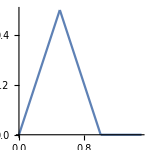

```mathematica
Plot[f[x],{x,0,1.5},AspectRatio->Automatic,ImageSize->150]
```

I was able to use WolframDocumentation, an article called tutorial/NDSolveWhenEvents which has some good info. I guess it sometimes helps to write a function that incorporates the Piecewise structure, but which can be called by a single symbol.

```mathematica
g1[x_,t_]=x;
g2[x_,t_]=1-x;
g[x_,t_]=If[x<0.5,g1[x,t],g2[x,t]];
```

Though the tutorial did not tell me to do so, using Dirichlet conditions occurred to me as one way to do it. The try below shows what it looked like. However, the next cell down, bsol2, shows a better way for this problem, and bsol is only here for historical interest.

```mathematica
bsol=First[u/. NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],DirichletCondition[u[x,t]==g[x,t],t==0&&0≤x<0.5],DirichletCondition[u[x,t]==0,x==0&&t==0],DirichletCondition[u[x,t]==g[x,t],x≥0.5&&t≥0]},u,{x,0,1},{t,0,1},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->15,MaxStepSize->0.002]]
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

After surfing around on a day when StackExchange was down, I found an old post http://forums.wolfram.com/mathgroup/archive/2008/Sep/msg00458.html from 2008 that showed putting Piecewise right into the NDSolve expression without apologies. So I tried it as below.

```mathematica
bsol2=First[u/. NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],u[x,0]==Piecewise[{{x,0≤x<0.5},{1-x,0.5≤x≤1}}],u[0,t]==0,u[1,t]==0},u,{x,0,1},{t,0,1},AccuracyGoal->12,WorkingPrecision->MachinePrecision,MaxStepSize->0.1]]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

And the First formulation allows me to conveniently plot it. This is a nicer plot than the one for the expression with g[x].

```mathematica
wiwp=Plot3D[bsol2[x,t],{x,0,1},{t,0,1},ImageSize->250,AspectRatio->Automatic,ViewPoint->{4000, 2000, 6000.},AxesLabel->Automatic]
```

-Graphics3D-

And I can build a table with solution values. As the problem specifies, the h step size is 0.2 and the k step size is 0.02. The table values are difficult to interpret.

```mathematica
TableForm[Table[bsol2[h,k],{h,0,1,0.4},{k,0,0.08,0.02}]]
```

0. | 0. | 0. | 0. | 6.77626×10^-21
0.4 | 0.320886 | 0.260491 | 0.213326 | 0.17503
0.2 | 0.188294 | 0.15928 | 0.131562 | 0.108129

The text answers for t=0.04 have 0.156 and 0.254, for t=0.08 the text lists 0.105 and 0.170. If the individual sets were flipped around, or the above table (third column) viewed from bottom going up, they would roughly agree. Assuming the explanation just made is acceptable, the results are not too bad. But maybe I need to check the performance of FEM on the same job. (This check I just made, and, the result being just the same as the above, I deleted it.)

8. In a laterally insulated bar of length 1 let the initial temperature be f[x] = x if 0 ≤  x < 0.5, f[x] = 1 - x if 0.5 ≤ x ≤ 1. Let (1) and (3) hold. Apply the explicit method with h = 0.2, k = 0.01, 5 steps. Can you expect the solution to satisfy u[x,t] = u[1 - x, t] for all t?

9.  Solve problem 8 with f[x] = x if 0 ≤ x ≤ 0.2, f[x] = 0.25(1 - x) if 0.2 < x ≤ 1, the other data being as before.

Here I use forthright identification of the function f[x] as piece-wise and get away with it, without stating any certain method for use with NDSolve. That is, no special modifications or adaptations are necessary.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Piecewise[{{x, 0≤x<0.2}, {0.25(1-x), 0.2≤x≤1}}]
```

Piecewise[{{x, 0≤x<0.2}, {0.25 (1-x), 0.2≤x≤1}, {0, True}}]

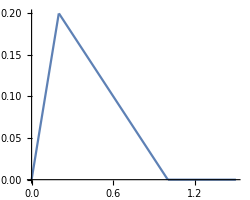

```mathematica
Plot[f[x],{x,0,1.5},AspectRatio->Automatic,ImageSize->250]
```

As before, I will not actually use the g[x] function here, merely show what they would look like for this problem.

```mathematica
g1[x_,t_]=x;
g2[x_,t_]=.25(1-x);
g[x_,t_]=If[x<0.2,g1[x,t],g2[x,t]];
```

Again, below, the addition of enhancing factors in the NDSolve expression is cheap. However, the difference in the solution between step size 0.1 and 0.001 is in the 5th decimal place, so it is not really worth putting in the smaller step size. Mathematica gives me one warning message, but then goes ahead and does the calculation, without freezing.

```mathematica
bsol2=First[u/. NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],u[x,0]==Piecewise[{{x,0≤x<0.2},{0.25(1-x),0.2≤x≤1}}],u[0,t]==0,u[1,t]==0},u,{x,0,1},{t,0,1},AccuracyGoal->12,WorkingPrecision->MachinePrecision,MaxStepSize->0.1]]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

```mathematica
wiwp=Plot3D[bsol2[x,t],{x,0,1},{t,0,1},ImageSize->250,AspectRatio->Automatic,ViewPoint->{4000, 2000, 6000.},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
TableForm[Table[bsol2[h,k],{h,0,1.0,0.2},{k,0,0.05,0.01}]]
```

0. | 0. | 0. | 0. | 0. | 0.
0.2 | 0.129594 | 0.102395 | 0.0844395 | 0.0715155 | 0.061685
0.15 | 0.143718 | 0.129259 | 0.114964 | 0.102247 | 0.0911765
0.1 | 0.0998782 | 0.097881 | 0.0934618 | 0.0876805 | 0.0813476
0.05 | 0.0499996 | 0.0499048 | 0.049288 | 0.0478799 | 0.0457676
0. | 0. | 0. | 0. | 0. | 0.

The values in the table are similar to the answer in the text (last column). For info, the text answer is 0, 0.06279, 0.09336, 0.08364, 0.04707,  0.

Crank-Nicolson method

11.  Solve problem 9 by (9) with h = 0.2, 2 steps. Compare with exact values obtained from the series in section 12.5  (2 terms)  with suitable coefficients.

There are some good, recent notebooks on numerical Mathematica at https://sites.google.com/site/chemengwithmathematica/home/numerical-methods. The Crank-Nicolson is under Numerical Methods for PDEs, and some code used later on is taken from that notebook. BGHiggins is the author. The code was not well adapted to the present problem, so I removed it. But it is used in problem 15. In its place is a FEM version which I believe works fairly well.

```mathematica
Clear["Global`*"]
```

```mathematica
uif=First[u/.NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],u[x,0]==Piecewise[{{x,0≤x<0.2},{0.25(1-x),0.2≤x≤1}}],u[0,t]==u[1,t]==0},u,{x,0,1},{t,0,1},Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}},AccuracyGoal->12,WorkingPrecision->MachinePrecision,MaxStepFraction->0.001]]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

```mathematica
Plot3D[uif[x,t],{x,0,1},{t,0,1},AxesLabel->Automatic,ImageSize->250,ViewPoint->{4000, 2000, 6000.}]
```

-Graphics3D-

```mathematica
TableForm[Table[uif[h,k],{h,0,1.0,0.2},{k,0.03,0.08,0.01}]]
```

0. | 0. | 0. | 0. | 0. | 0.
0.0844303 | 0.0715163 | 0.0616857 | 0.0538905 | 0.0475197 | 0.0421898
0.114969 | 0.102245 | 0.0911758 | 0.0815588 | 0.0731626 | 0.0657838
0.0934634 | 0.0876817 | 0.0813474 | 0.0749336 | 0.0686977 | 0.0627752
0.0492862 | 0.0478801 | 0.0457683 | 0.0431678 | 0.0402949 | 0.0373216
0. | 0. | 0. | 0. | 0. | 2.71051×10^-20

I think the redirections on this problem may have messed things up for the designation of the desired answer. The answer in the text for exact values for “Step 2” is as follows: 0, 0.0422, 0.0658, 0.0628, 0.0373, 0. These numbers should be compared with the last column above, with which their resemblance is very suggestive.

13 - 15  Solve (1) - (3) by Crank-Nicolson with r = 1  (5 steps), where

13. f[x_]= Piecewise[{{5 x, 0≤x<0.25}, {1.25(1-x), 0.25≤x≤1}}]  , h = 0.2

Since k = r h^2, k = 0.04.

```mathematica
Clear["Global`*"]
```

The Crank-Nicolson method is one I haven’t been able to get to work well with Piecewise functions. I substitute a FEM method approach here. It doesn’t do too badly. The current problem’s equation for f[x] allows setting the MaxCellMeasure quite small.

```mathematica
uif=First[u/.NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],u[x,0]==Piecewise[{{5x,0≤x<0.25},{1.25(1-x),0.25≤x≤1}}],u[0,t]==u[1,t]==0},u,{x,0,1},{t,0,1},Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}},AccuracyGoal->12,WorkingPrecision->MachinePrecision,MaxStepFraction->0.001]]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

The plot doesn’t look too ragged.

```mathematica
Plot3D[uif[x,t],{x,0,1},{t,0,1},AxesLabel->Automatic,ImageSize->250,ViewPoint->{4000, 2000, 6000.}]
```

-Graphics3D-

```mathematica
TableForm[Table[uif[h,k],{h,0.2,0.8,0.2},{k,0,0.05,0.01}]]
```

1. | 0.669005 | 0.525685 | 0.432009 | 0.365051 | 0.31432
0.75 | 0.729531 | 0.657158 | 0.584413 | 0.519525 | 0.46307
0.5 | 0.500162 | 0.492285 | 0.471403 | 0.442987 | 0.411421
0.25 | 0.250005 | 0.249805 | 0.247297 | 0.240828 | 0.230672

The table above is not in excellent agreement with the text answer, with some values low, others high, in the 5th column, the one sought. The text answers there are 0.3301, 0.5706, 0.4522, 0.2380.

15.  f[x_]=x(1-x) , h=0.2

This problem, involving as it does a continuous function for f[x], gives me an opportunity to authenticate  the accuracy of the CrankNicolson, using Professor Higgins’s code.

```mathematica
Clear["Global`*"]
```

```mathematica
LX=1;
NP=80;
Δx=LX/(NP-1)//N;
GridRules=Table[x[i]->(i-1)Δx,{i,1,NP}];
f[x_]:=x(1-x)
```

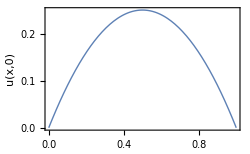

```mathematica
Plot[f[x],{x,0,1},PlotStyle->Thickness[0.004],Frame->True,FrameLabel->{Style["x",16],Style["u(x,0)",16]},ImageSize->250]
```

```mathematica
𝕂=1;
Δt= Δx^2;
λ= 𝕂 Δt/Δx^2;
```

```mathematica
eqnTemplate:=λ u2[i+1]-2(1+λ)u2[i]+λ u2[i-1]==-λ u1[i+1]-2(1-λ)u1[i]-λ u1[i-1]
FDEqns=Table[eqnTemplate,{i,2,NP-1}]/.{u2[1]->0,u2[NP]->0,u1[1]->0,u1[NP]->0};
ICvar=Union[Cases[FDEqns, u1[_],∞]];
var=Union[Cases[FDEqns, u2[_],∞]];
```

Below I reduced NT from 500 to 250 in order to access the plot for t = 0.04.

```mathematica
For[NT=250;ICond=Table[u1[i]->f[x]/.x->x[i],{i,2,NP-1}]/.GridRules;
j=1,j<NT,{b,A}=CoefficientArrays[FDEqns/.ICond,var];sol=LinearSolve[A,-b];ICond=Thread[ICvar->sol];j++]
```

According to the text answer, the solution for the first step of h = 0.2 is 0.1018, at t = 0.04, and that looks pretty close to the plot value. To be more exact, the two closest values in hvc below bracket 0.1018, are: {0.189873,0.0980386},{0.202532,0.103677}, from which the interpolated function value for x = 0.2 would be 0.1025, reasonably close.

```mathematica
hvc=Transpose[{Table[x[i],{i,1,NP}]/.GridRules,Append[Prepend[sol,0],0]}];
```

Now I’m going to try to check the solution using a series solution, which is also provided by the same CN notebook of Higgins. If I try to use the continuous function f[x]=x, then the appropriate parameters for this problem (doing just f1) are

k = 1, L = 0.2, f (x) = x;
Hence, the mathematical statement of the example problem solved by the finite difference method is

(∂u)/(∂t)=𝕂(∂^2 u)/(∂x^2),    0<x<L, t>0
IC: 	u(x,0)=f(x)
BC1:	u(0,t)=0
BC2:	u(L,t)=0

The solution found by separation of variables is

u(x,t)=∑_(n=1)^∞ b_n Sin(n π x/L)e^(-𝕂(n π/L)^2 t)

where the Fourier coefficients are given by

b_n=2/L∫_0^L f(x)Sin(n π x/L)ⅆx

The Fourier coefficients and the resulting plot are given below.

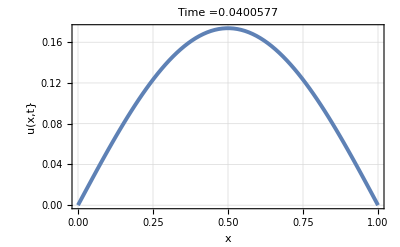

```mathematica
fd=ListPlot[Transpose[{Table[x[i],{i,1,NP}]/.GridRules,Append[Prepend[sol,0],0]}],Joined->True,Frame->True,PlotStyle->Thickness[0.007],FrameLabel->{Style["x",16],Style["u(x,t}",16]},PlotLabel->"Time ="<>ToString[NT Δt],GridLines->Automatic]
```

And now the series plot.

```mathematica
bb[n_]:=bb[n]=2 NIntegrate[ f[x] Sin[n Pi x],{x,0,1}];
Table[bb[n],{n,1,30}];
𝕂=1;
F[x_,t_,n_]:=Sum[bb[j] Sin[j Pi x] Exp[-𝕂 j^2 Pi^2 t],
				{j,1,n}];
fs=Plot[F[x,NT Δt,20],{x,0,1},PlotRange->Automatic,Frame->True,PlotStyle->{White,Thickness[0.003]},FrameLabel->{Style["x",16],Style["u(x,t}",16]},PlotLabel->"Time ="<>ToString[NT Δt]];
```

When the series version plot is overlaid on top of the solution version plot,  a close agreement (though not perfect) can be seen.

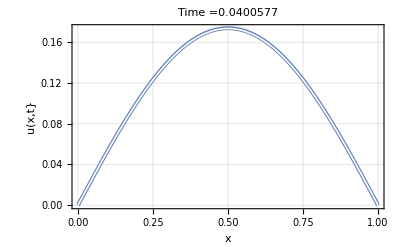

```mathematica
Show[fd,fs]
```

Following up with more solutions to the current problem. Below, I dust off the method mentioned in problem 9 as an alternative route to Crank-Nicolson.

```mathematica
Clear["Global`*"]
```

```mathematica
cnsol=First[u/. NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],DirichletCondition[u[x,t]==x(1-x),t==0&&0≤x<1],DirichletCondition[u[x,t]==0,x==0&&t==0],DirichletCondition[u[x,t]==0,x==1&&0≤t<1]},u,{x,0,1},{t,0,1},Method->{"DoubleStep",Method->CrankNicolson},PrecisionGoal->16,AccuracyGoal->16,WorkingPrecision->20,MaxStepSize->0.001]]
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

```mathematica
pc=Plot3D[cnsol[x,t],{x,0,1},{t,0,1},ImageSize->250,AspectRatio->Automatic,ViewPoint->{4000, -7000, 6000.},AxesLabel->Automatic]
```

-Graphics3D-

The third column of the table below would be the one I would try to match with text answer. The second and third entries are not terrible, but not great either.

```mathematica
TableForm[Table[cnsol[h,k],{h,0,1.0,0.3},{k,0,0.06,0.02}]]
```

0. | 0.112802 | 0.153099 | 0.15324
0.21 | 0.184225 | 0.170901 | 0.165557
0.24 | 0.201446 | 0.168982 | 0.144972
0.09 | 0.0679211 | 0.0536557 | 0.0452542

I’m not sure if that last one really executed the Crank-Nicolson method, though it was called for. A firmer basis for believing CN is being seen in action is contained in the next blocks.

```mathematica
Clear["Global`*"]
```

```mathematica
Options[CrankNicolson]={MaxIterations->5,Tolerance->Automatic};
CrankNicolson/:NDSolve`InitializeMethod[CrankNicolson,stepmode_,sd_,rhs_,state_,OptionsPattern[CrankNicolson]]:=Module[{prec,rtol,maxit},maxit=OptionValue[MaxIterations];
prec=state@"WorkingPrecision";
rtol=OptionValue[Tolerance];
If[rtol===Automatic,rtol=10^(-prec*3/4)];
CrankNicolson[maxit,rtol]]

CrankNicolson[maxit_,rtol_]["Step"[f_,h_,t0_,x0_,f0_]]:=Module[{J,LU,t1=t0+h,x1,f1,residual,err,done=False,tol=rtol,count=0},x1=x0+h f0;
f1=f[t1,x1];
x1=x0+(h/2) (f0+f1);
J=f["JacobianMatrix"[t1,x1]];
LU=IdentityMatrix[Length[x1],SparseArray]-(h/2) J;
LU=LinearSolve[LU];
While[(count≤maxit)&&!done,f1=f[t1,x1];
residual=x1-x0-(h/2)*(f0+f1);
err=Norm[residual,Infinity];
If[err<tol,done=True
(*else*),x1=x1-LU[residual];
count++;]];
If[count>maxit,Message[CrankNicolson::cvmit,maxit];
x1=$Failed];
{x1,f1}];

CrankNicolson[___]["StepInput"]={"F"["T","X"],"H","T","X","XP"};
CrankNicolson[___]["StepOutput"]={"X","XP"};
CrankNicolson[___]["DifferenceOrder"]:=2;
CrankNicolson[___]["StepMode"]:="Fixed";
```

Here is included the test sample from the documentation. Note below that the step size in the example function is 0.1. I will change this later.

```mathematica
NDSolve[{x''[t]+x[t]==0,x[0]==1,x'[0]==0},x,{t,0,2 π},Method->{"FixedStep","StepSize"->.1,Method->{CrankNicolson,MaxIterations->1,Tolerance->$MachineEpsilon}}]
```

{{x→InterpolatingFunction[{{0., 6.28319}}, <>]}}

```mathematica
TableForm[Table[cns[h,k],{h,0,1.0,0.3},{k,0,0.06,0.02}]];
```

Now that I have tried the example and all seems to be working, I will plug in the problem function. The lines shown reflect some tinkering, by adding the enhancing options and reducing the step size. Smaller step size was very cheap, almost seemed free.

```mathematica
cnz=First[u/.NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],u[x,0]==x(1-x),u[0,t]==0,u[1,t]==0},u,{x,0,1},{t,0,1},Method->{"FixedStep","StepSize"->.001,Method->{CrankNicolson}},PrecisionGoal->9,AccuracyGoal->9,WorkingPrecision->12]]
```

InterpolatingFunction[{{0, 1.00000000000}, {0, 1.}}, <>]

The plot I get is much smoother than some previous ones. Oddly, it looks symmetrical across the x interval lines, with x = 0.5 as the fulcrum.

```mathematica
cnn=Plot3D[cnz[x,t],{x,0,1},{t,0,1},ImageSize->250,AspectRatio->Automatic,ViewPoint->{4000, 7000, 6000.},AxesLabel->Automatic]
```

-Graphics3D-

In the table, the h values go down vertically, the k values go across horizontally. The third column is t=0.04, and it looks more or less acceptable.

```mathematica
tableW=TableForm[Table[cnz[h,k],{h,0,1.0,0.2},{k,0,0.06,0.02}]]
```

0. | 0. | 0. | 0.
0.16 | 0.126025 | 0.102449 | 0.0839276
0.24 | 0.200478 | 0.165185 | 0.135699
0.24 | 0.200478 | 0.165185 | 0.135699
0.16 | 0.126025 | 0.102449 | 0.0839276
0. | 0. | 0. | 0.

The grid below shows reasonable agreement with the text answer.

```mathematica
Grid[{{"tableW","text ans"},{0,0},{0.102449,0.1018},{0.165185,0.1673},{0.165185,0.1673},{0.102449,0.1018},{0,0}},Frame->All]
```

tableW | text ans
0 | 0
0.102449 | 0.1018
0.165185 | 0.1673
0.165185 | 0.1673
0.102449 | 0.1018
0 | 0